```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## -1/3 < m < 0

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=-1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

plt1=Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

$Aborted

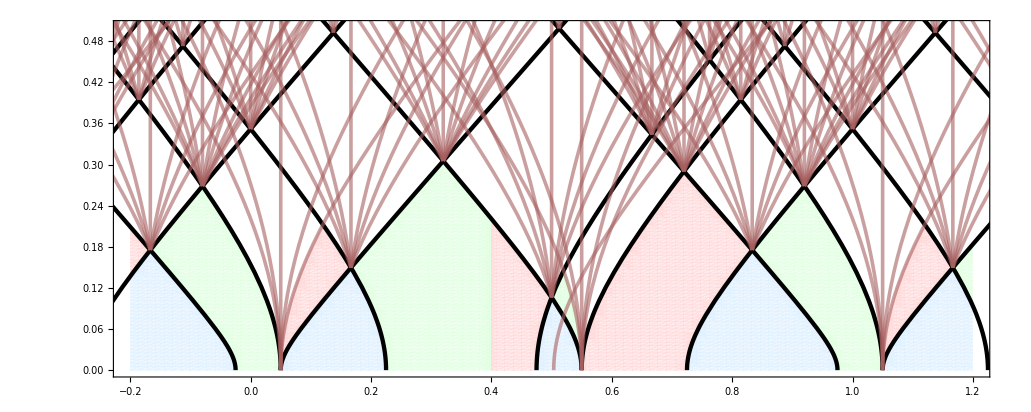

```mathematica
Show[domainI,domainII,domainBr,temp,AspectRatio->Automatic]
```

## 0 < m < 1/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,0},{2,1},{3,2},{4,2},{5,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

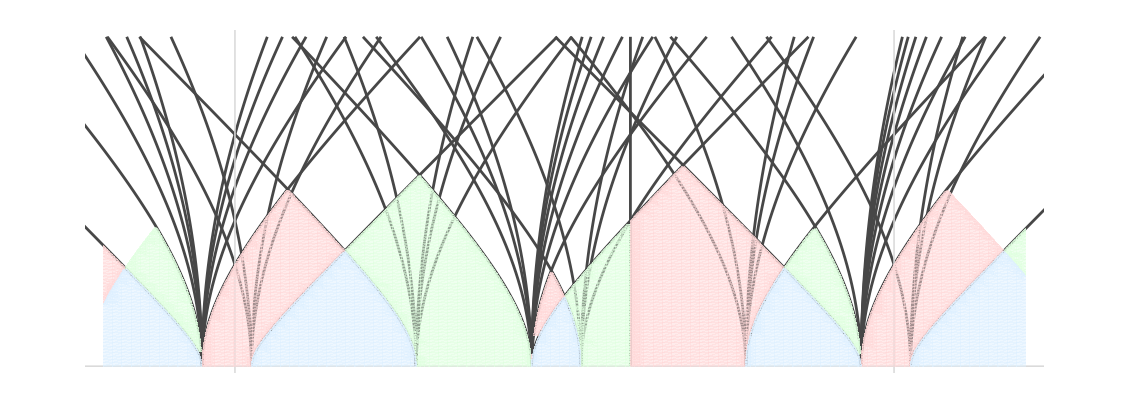

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

## 1/3 < m < 2/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,1},{2,1},{3,2},{4,3},{5,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

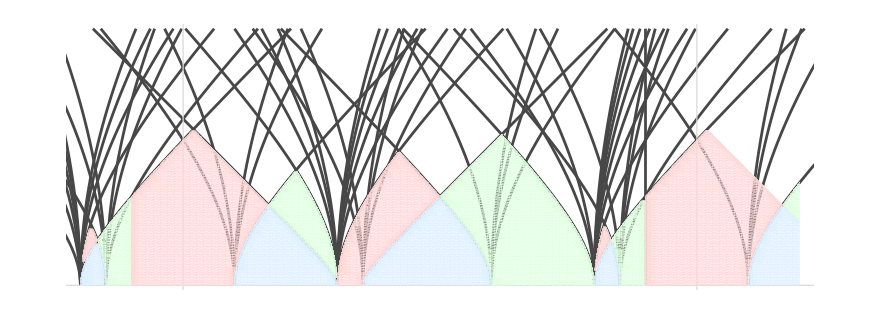

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=4/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

```mathematica
SpectralFlow[GV[0,-1,-1/2]/.repCh,{-3,-2}]
```

{0,0,-1,1/2}

```mathematica
Ch[0,0]-Ch[0,1]/.repCh
```

{0,0,-1,1/2}

```mathematica
With[{m=2/5},Flatten@Table[k+{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}, {k,0,0}]]
```

{1/10,7/20,3/10,3/5,9/10,17/20,4/5}

```mathematica
{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}
SortBy[%, #/.{m->2/5}&]
```

{m/4,(1+m)/4,(1-m)/2,(2+m)/4,1/2+m,(3+m)/4,1-m/2}

{m/4,(1-m)/2,(1+m)/4,(2+m)/4,1-m/2,(3+m)/4,1/2+m}

```mathematica
DSZ[Ch[1,1],-Ch[0,1]]/.repCh
```

2

```mathematica
DSZ[Ch[2,1],-Ch[0,1]]/.repCh
```

4

```mathematica
ChernToCh[2Ch[1,1]-Ch[0,1]/.repCh]
```

Ch[2,1]

```mathematica
DSZ[Ch[1,1],-Ch[2,2]]/.repCh
```

-3

```mathematica
DSZ[Ch[3,2],-Ch[2,2]]/.repCh
```

2

```mathematica
SpectralFlow[{0,0,1,ch2},{3k,2k}]
```

{0,0,1,ch2+k}

## Redo

#### -1/3 < m < 0

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
(*Example usage*)
MaTeX["\\textcolor{gamcolor}{\\textbf{Hello from amsart (11pt)}}"]
```

-Graphics-

```mathematica
ClearAll[AsBr,AsAI,AsAII];
AsBr[m_]:=<|"Coll"->CollBridgeland, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightBlue, "Label"->"Br"|>;
AsAI[m_]:=<|"Coll"->CollArcaraI, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-3)/3]}, {mf,1,5}], "Color"->LightGreen, "Label"->"ArI"|>;
AsAII[m_]:=<|"Coll"->CollArcaraII, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightRed,"Label"->"ArII"|>;
```

```mathematica
MakeDomain[AsColl_, m_]:=Table[QDomain[SpectralFlow[AsColl["Coll"]/.repCh, spec], m,AsColl["Label"]<>"⊗"<>ToString[spec], PlotStyle->Directive[AsColl["Color"], Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {spec, AsColl["SpectralFlows"]}];
```

```mathematica
ticks=Thread[{#/.m->-1/10, MaTeX[Simplify[#]]}]&@Flatten[Table[{(m+k)/4, (k-m)/2, -1/2-k+m}, {k,-5,5}]];
```

```mathematica
With[{m=-1/10, psi=0, coll=CollInitial[[3]], L=5, xmin=-1, xmax=2},
charges=Flatten[Table[s gam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{gam, coll},{k,-L,L},{s,{-1,1}}]];
charges=Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]];
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, {g, Last[Initials[g/.repCh,m, "Verbose"->False]]}], {g, charges}];

othercharges=Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]];
othercharges=Select[othercharges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&&!MemberQ[charges,#]&];
othercharges=Join[othercharges, {GV[1,0,0], GV[1,0,1], GV[1,0,2]}];
otherrays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, {g, Last[Initials[g/.repCh,m, "Verbose"->False]]}], {g, othercharges}];

dBr=MakeDomain[AsBr[m],m];
dAI=MakeDomain[AsAI[m],m];
dAII=MakeDomain[AsAII[m],m];
]
```

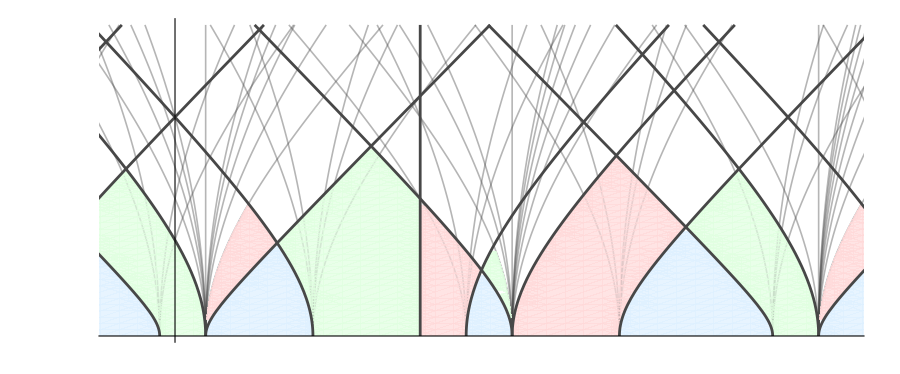

```mathematica
plt=Show[{
ParametricPlot[otherrays, {t,0,0.5},
PlotStyle->Directive[Thickness[.0013],RGBColor[0.28, 0.28, 0.28], Opacity[.4]]
],
dBr,
dAI,
dAII,
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28]
](*,
Graphics[{Red, GamLabel[-Ch[-1,-1], -1/10, 0, "\\mathcal{O}(-1,-1)[1]", .4]}]*)
},
PlotRange->{{-.1, 1.1},{0,0.5}},
AspectRatio->Automatic,
Frame->False,
Axes->{True,False},
Ticks->{ticks,None},
ImageSize->900
]
```

```mathematica
charges
```

{-Ch[-3,-2],-Ch[0,0],Ch[0,0],-Ch[3,2],Ch[3,2],Ch[6,4],-Ch[-2,-2],Ch[-2,-2],-Ch[1,0],Ch[1,0],-Ch[4,2],Ch[4,2],-Ch[-2,-1],Ch[-2,-1],-Ch[1,1],Ch[1,1],-Ch[4,3],Ch[4,3],-Ch[-1,-1],Ch[-1,-1],-Ch[2,1],Ch[2,1],-Ch[5,3],Ch[5,3],GV[0,1,3/2],GV[0,1,1/2],GV[0,1,-1/2]}

```mathematica
othercharges
```

{-Ch[-5,-2],-Ch[-5,-1],-Ch[-5,0],-Ch[-5,1],-Ch[-5,2],-Ch[-5,3],-Ch[-4,-5],-Ch[-4,-2],-Ch[-4,-1],-Ch[-4,0],-Ch[-4,1],-Ch[-4,2],-Ch[-4,3],-Ch[-3,-5],-Ch[-3,-4],-Ch[-3,-3],-Ch[-3,-1],-Ch[-3,0],-Ch[-3,1],-Ch[-3,2],-Ch[-3,3],-Ch[-2,-5],-Ch[-2,-4],-Ch[-2,-3],-Ch[-2,0],-Ch[-2,1],-Ch[-2,2],-Ch[-2,3],-Ch[-1,-5],-Ch[-1,-4],-Ch[-1,-3],-Ch[-1,-2],Ch[-1,-2],-Ch[-1,0],Ch[-1,0],-Ch[-1,1],Ch[-1,1],-Ch[-1,2],-Ch[-1,3],-Ch[0,-5],-Ch[0,-4],-Ch[0,-3],-Ch[0,-2],Ch[0,-2],-Ch[0,-1],Ch[0,-1],-Ch[0,1],Ch[0,1],-Ch[0,2],Ch[0,2],-Ch[0,3],Ch[0,3],-Ch[1,-5],-Ch[1,-4],-Ch[1,-3],-Ch[1,-2],Ch[1,-2],-Ch[1,-1],Ch[1,-1],-Ch[1,2],Ch[1,2],-Ch[1,3],Ch[1,3],Ch[1,4],Ch[1,5],-Ch[2,-4],-Ch[2,-3],-Ch[2,-2],Ch[2,-2],-Ch[2,-1],Ch[2,-1],-Ch[2,0],Ch[2,0],-Ch[2,2],Ch[2,2],-Ch[2,3],Ch[2,3],Ch[2,4],Ch[2,5],-Ch[3,-2],Ch[3,-2],-Ch[3,-1],Ch[3,-1],-Ch[3,0],Ch[3,0],-Ch[3,1],Ch[3,1],-Ch[3,3],Ch[3,3],Ch[3,4],Ch[3,5],Ch[4,-2],Ch[4,-1],-Ch[4,0],Ch[4,0],-Ch[4,1],Ch[4,1],Ch[4,4],Ch[4,5],Ch[5,-2],Ch[5,-1],Ch[5,0],Ch[5,1],-Ch[5,2],Ch[5,2],Ch[5,4],Ch[5,5],GV[1,0,0],GV[1,0,1],GV[1,0,2]}

```mathematica
Initials[#,-1/10, "Verbose"->False]&/@(charges/.repCh)
```

{{-19/20,0},{1/20,0},{-1/40,0},{21/20,0},{39/40,0},{79/40,0},{-21/40,0},{-19/20,0},{19/40,0},{1/20,0},{59/40,0},{21/20,0},{-9/20,0},{-31/40,0},{11/20,0},{9/40,0},{31/20,0},{49/40,0},{-11/40,0},{-9/20,0},{29/40,0},{11/20,0},{69/40,0},{31/20,0},{7/5,0},{2/5,0},{-3/5,0}}

```mathematica
{#, Last[Initials[#/.repCh,-1/10, "Verbose"->False]]}&/@othercharges
```

{{-Ch[-5,-2],2},{-Ch[-5,-1],3},{-Ch[-5,0],5},{-Ch[-5,1],6},{-Ch[-5,2],8},{-Ch[-5,3],9},{-Ch[-4,-5],Missing[DoesNotReachBdy]},{-Ch[-4,-2],1},{-Ch[-4,-1],2},{-Ch[-4,0],4},{-Ch[-4,1],5},{-Ch[-4,2],7},{-Ch[-4,3],8},{-Ch[-3,-5],Missing[DoesNotReachBdy]},{-Ch[-3,-4],Missing[DoesNotReachBdy]},{-Ch[-3,-3],Missing[DoesNotReachBdy]},{-Ch[-3,-1],1},{-Ch[-3,0],3},{-Ch[-3,1],4},{-Ch[-3,2],6},{-Ch[-3,3],7},{-Ch[-2,-5],Missing[DoesNotReachBdy]},{-Ch[-2,-4],Missing[DoesNotReachBdy]},{-Ch[-2,-3],Missing[DoesNotReachBdy]},{-Ch[-2,0],2},{-Ch[-2,1],3},{-Ch[-2,2],5},{-Ch[-2,3],6},{-Ch[-1,-5],Missing[DoesNotReachBdy]},{-Ch[-1,-4],Missing[DoesNotReachBdy]},{-Ch[-1,-3],Missing[DoesNotReachBdy]},{-Ch[-1,-2],Missing[DoesNotReachBdy]},{Ch[-1,-2],1},{-Ch[-1,0],1},{Ch[-1,0],Missing[DoesNotReachBdy]},{-Ch[-1,1],2},{Ch[-1,1],Missing[DoesNotReachBdy]},{-Ch[-1,2],4},{-Ch[-1,3],5},{-Ch[0,-5],Missing[DoesNotReachBdy]},{-Ch[0,-4],Missing[DoesNotReachBdy]},{-Ch[0,-3],Missing[DoesNotReachBdy]},{-Ch[0,-2],Missing[DoesNotReachBdy]},{Ch[0,-2],2},{-Ch[0,-1],Missing[DoesNotReachBdy]},{Ch[0,-1],1},{-Ch[0,1],1},{Ch[0,1],Missing[DoesNotReachBdy]},{-Ch[0,2],3},{Ch[0,2],Missing[DoesNotReachBdy]},{-Ch[0,3],4},{Ch[0,3],Missing[DoesNotReachBdy]},{-Ch[1,-5],Missing[DoesNotReachBdy]},{-Ch[1,-4],Missing[DoesNotReachBdy]},{-Ch[1,-3],Missing[DoesNotReachBdy]},{-Ch[1,-2],Missing[DoesNotReachBdy]},{Ch[1,-2],3},{-Ch[1,-1],Missing[DoesNotReachBdy]},{Ch[1,-1],2},{-Ch[1,2],2},{Ch[1,2],Missing[DoesNotReachBdy]},{-Ch[1,3],3},{Ch[1,3],Missing[DoesNotReachBdy]},{Ch[1,4],Missing[DoesNotReachBdy]},{Ch[1,5],Missing[DoesNotReachBdy]},{-Ch[2,-4],Missing[DoesNotReachBdy]},{-Ch[2,-3],Missing[DoesNotReachBdy]},{-Ch[2,-2],Missing[DoesNotReachBdy]},{Ch[2,-2],4},{-Ch[2,-1],Missing[DoesNotReachBdy]},{Ch[2,-1],3},{-Ch[2,0],Missing[DoesNotReachBdy]},{Ch[2,0],1},{-Ch[2,2],1},{Ch[2,2],Missing[DoesNotReachBdy]},{-Ch[2,3],2},{Ch[2,3],Missing[DoesNotReachBdy]},{Ch[2,4],Missing[DoesNotReachBdy]},{Ch[2,5],Missing[DoesNotReachBdy]},{-Ch[3,-2],Missing[DoesNotReachBdy]},{Ch[3,-2],5},{-Ch[3,-1],Missing[DoesNotReachBdy]},{Ch[3,-1],4},{-Ch[3,0],Missing[DoesNotReachBdy]},{Ch[3,0],2},{-Ch[3,1],Missing[DoesNotReachBdy]},{Ch[3,1],1},{-Ch[3,3],1},{Ch[3,3],Missing[DoesNotReachBdy]},{Ch[3,4],Missing[DoesNotReachBdy]},{Ch[3,5],Missing[DoesNotReachBdy]},{Ch[4,-2],6},{Ch[4,-1],5},{-Ch[4,0],Missing[DoesNotReachBdy]},{Ch[4,0],3},{-Ch[4,1],Missing[DoesNotReachBdy]},{Ch[4,1],2},{Ch[4,4],Missing[DoesNotReachBdy]},{Ch[4,5],Missing[DoesNotReachBdy]},{Ch[5,-2],7},{Ch[5,-1],6},{Ch[5,0],4},{Ch[5,1],3},{-Ch[5,2],Missing[DoesNotReachBdy]},{Ch[5,2],1},{Ch[5,4],Missing[DoesNotReachBdy]},{Ch[5,5],Missing[DoesNotReachBdy]},{GV[1,0,0],0},{GV[1,0,1],0},{GV[1,0,2],0}}

```mathematica
(*FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "LVRasterize_m_m1_10.pdf"], %]*)
```

/Users/rishi/Developer/localf1/figures/LargeVolume/LVRasterize_m_m1_10.pdf

```mathematica
GamLabel[gam_, m_, psi_, string_, t0_]:=Module[{r=(gam/.repCh)[[1]]},Text[MaTeX["\\textcolor{gamcolor}{"<>string<>"}"], {Rays[gam/.repCh, #,psi,m], #}&[t0], {0,-1}, -Sign[If[r!=0,r,-1]]Normalize[{D[Rays[gam/.repCh, t,psi,m],t]/.{t->t0}, 1}]]];
```

```mathematica
labels=With[{m=-1/10,psi=0},{
GamLabel[Ch[0,0], m, psi, "\\mathcal{O}(0,0)", .1],
GamLabel[Ch[1,0], m, psi, "\\mathcal{O}(1,0)", .33],
GamLabel[Ch[1,1], m, psi, "\\mathcal{O}(1,1)", .43],
GamLabel[-Ch[-1,-1], m, psi, "\\mathcal{O}(-1,-1)[1]", .4],
GamLabel[Ch[2,1], m, psi, "\\mathcal{O}(2,1)", .4],
GamLabel[-Ch[0,0], m, psi, "\\mathcal{O}(0, 0)[1]", .35],
GamLabel[Ch[3,2], m, psi, "\\mathcal{O}(3, 2)", .44],
GamLabel[-Ch[1,0], m, psi, "\\mathcal{O}(1, 0)[1]", .4],
GamLabel[-Ch[1,1], m, psi, "\\mathcal{O}(1, 1)[1]", .43],
GamLabel[Ch[4,2], m, psi, "\\mathcal{O}(4, 2)", .35],
GamLabel[Ch[4,3], m, psi, "\\mathcal{O}(4, 3)", .4],
GamLabel[-Ch[2,1], m, psi, "\\mathcal{O}(2, 1)[1]", .4],
GamLabel[-Ch[3,2], m, psi, "\\mathcal{O}(3, 2)[1]", .1],
GamLabel[GV[0,1,1/2], m, psi, "GV\\left(0,1,\\tfrac12\\right)", .1],
(* Quiver domains for CollBridgeland *)
Text[MaTeX["\\mathcal{C}"], {-.12,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(1,1)"], {.14,.04}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(2,1)"},Center, -.1], {.51, .04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(3,2)"], {.84,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(4,3)"], {1.12,.03}],
(* Quiver domains for CollArcaraI *)
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(1,0)"], {-.07,.16}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(2,1)"], {.3,.06}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(3,1)"},Center, -.1], {.53,.117}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(4,2)"], {.97,.1}],
(* Quiver domains for CollArcaraII *)
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes","\\mathcal{O}(1,1)"},Center, -.1], {0.123,.16}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(2,1)"], {.45,.1}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(3,2)"], {.67,.1}],
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes","\\mathcal{O}(4,3)"},Center, -.1], {1.12,.17}]
}];
plt1=Show[plt, Graphics[labels]]
```

-Graphics-

```mathematica
FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt1, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "Ras_LV_m_m1_10.pdf"], %]
```

/Users/rishi/Developer/localf1/figures/LargeVolume/Ras_LV_m_m1_10.pdf

```mathematica
Ch[1,0]-Ch[0,0]/.repCh
```

{0,1,0,0}

#### 0 < m < 1/3

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
(*Example usage*)
MaTeX["\\textcolor{gamcolor}{\\textbf{Hello from amsart (11pt)}}"]
```

-Graphics-

```mathematica
ClearAll[AsBr,AsAI,AsAII];
AsBr[m_]:=<|"Coll"->CollBridgeland, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightBlue, "Label"->"Br"|>;
AsAI[m_]:=<|"Coll"->CollArcaraI, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-3)/3]}, {mf,1,5}], "Color"->LightGreen, "Label"->"ArI"|>;
AsAII[m_]:=<|"Coll"->CollArcaraII, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightRed,"Label"->"ArII"|>;
```

```mathematica
MakeDomain[AsColl_, m_]:=Table[QDomain[SpectralFlow[AsColl["Coll"]/.repCh, spec], m,AsColl["Label"]<>"⊗"<>ToString[spec], PlotStyle->Directive[AsColl["Color"], Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {spec, AsColl["SpectralFlows"]}];
```

```mathematica
ticks=Thread[{#/.m->1/10, MaTeX[Simplify[#]]}]&@Flatten[Table[{(m+k)/4, (k-m)/2, -1/2-k+m}, {k,-5,5}]];
```

```mathematica
With[{m=1/10, psi=0, coll=CollInitial[[1]], L=5, xmin=-1, xmax=2},
charges=Flatten[Table[s gam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{gam, coll},{k,-L,L},{s,{-1,1}}]];
charges=Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]];
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, {g, Last[Initials[g/.repCh,m, "Verbose"->False]]}], {g, charges}];

othercharges=Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]];
othercharges=Select[othercharges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&&!MemberQ[charges,#]&];
othercharges=Join[othercharges, {GV[1,0,0], GV[1,0,1], GV[1,0,2]}];
otherrays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, {g, Last[Initials[g/.repCh,m, "Verbose"->False]]}], {g, othercharges}];

dBr=MakeDomain[AsBr[m],m];
dAI=MakeDomain[AsAI[m],m];
dAII=MakeDomain[AsAII[m],m];
]
```

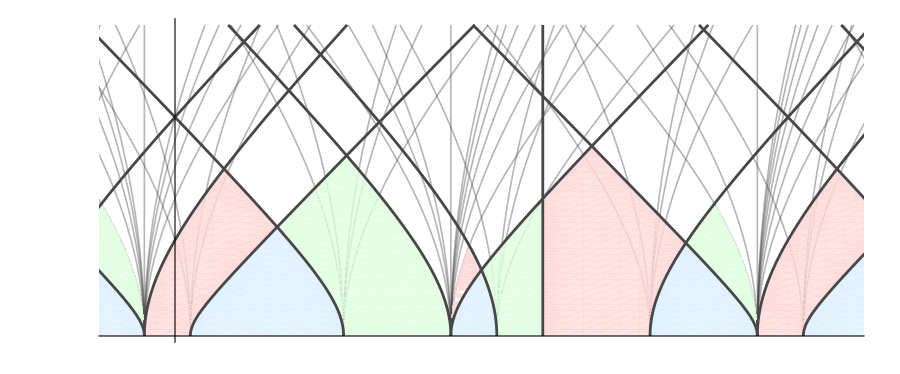

```mathematica
plt=Show[{
ParametricPlot[otherrays, {t,0,0.5},
PlotStyle->Directive[Thickness[.0013],RGBColor[0.28, 0.28, 0.28], Opacity[.4]]
],
dBr,
dAI,
dAII,
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28]
](*,
Graphics[{Red, GamLabel[-Ch[-1,-1], -1/10, 0, "\\mathcal{O}(-1,-1)[1]", .4]}]*)
},
PlotRange->{{-.1, 1.1},{0,0.5}},
AspectRatio->Automatic,
Frame->False,
Axes->{True,False},
Ticks->{ticks,None},
ImageSize->900
]
```

```mathematica
(*FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "LVRasterize_m_m1_10.pdf"], %]*)
```

/Users/rishi/Developer/localf1/figures/LargeVolume/LVRasterize_m_m1_10.pdf

```mathematica
GamLabel[gam_, m_, psi_, string_, t0_]:=Module[{r=(gam/.repCh)[[1]]},Text[MaTeX["\\textcolor{gamcolor}{"<>string<>"}"], {Rays[gam/.repCh, #,psi,m], #}&[t0], {0,-1}, -Sign[If[r!=0,r,-1]]Normalize[{D[Rays[gam/.repCh, t,psi,m],t]/.{t->t0}, 1}]]];
```

```mathematica
labels=With[{m=1/10,psi=0},{
GamLabel[Ch[0,0], m, psi, "\\mathcal{O}(0,0)", .08],
GamLabel[Ch[1,0], m, psi, "\\mathcal{O}(1,0)", .33],
GamLabel[Ch[1,1], m, psi, "\\mathcal{O}(1,1)", .43],
GamLabel[-Ch[-1,-1], m, psi, "\\mathcal{O}(-1,-1)[1]", .3],
GamLabel[-Ch[-1,0], m, psi, "\\mathcal{O}(-1,0)[1]", .33],
GamLabel[Ch[2,1], m, psi, "\\mathcal{O}(2,1)", .35],
GamLabel[Ch[2,2], m, psi, "\\mathcal{O}(2,2)", .25],
GamLabel[-Ch[2,2], m, psi, "\\mathcal{O}(2,2)[1]", .2],
GamLabel[-Ch[0,0], m, psi, "\\mathcal{O}(0, 0)[1]", .4],
GamLabel[Ch[3,2], m, psi, "\\mathcal{O}(3, 2)", .25],
GamLabel[-Ch[1,1], m, psi, "\\mathcal{O}(1, 1)[1]", .43],
GamLabel[Ch[4,3], m, psi, "\\mathcal{O}(4, 3)", .4],
GamLabel[-Ch[2,1], m, psi, "\\mathcal{O}(2, 1)[1]", .4],
GamLabel[-Ch[3,2], m, psi, "\\mathcal{O}(3, 2)[1]", .1],
GamLabel[GV[0,1,1/2], m, psi, "GV\\left(0,1,\\tfrac12\\right)", .3],
(* Quiver domains for CollBridgeland *)
Text[MaTeX["\\mathcal{C}"], {-.13,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(1,1)"], {.16,.04}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(2,2)"},Center, -.1], {.49, .04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(3,2)"], {.86,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(4,3)"], {1.11,.03}],
(* Quiver domains for CollArcaraI *)
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(1,0)"}, Center, -.1], {-.12,.16}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(2,1)"], {.35,.06}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(3,2)"},Center, -.1], {.56,.11}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(4,2)"}, Center, -.1], {.88,.15}],
(* Quiver domains for CollArcaraII *)
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(1,1)"], {0.08,.17}],
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes", "\\mathcal{O}(2,2)"}, Center, -.1], {.47,.11}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(3,2)"], {.7,.1}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(4,3)"], {1.08,.17}](**)
}];
plt1=Show[plt, Graphics[labels]]
```

-Graphics-

```mathematica
FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt1, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "Ras_LV_m_1_10.pdf"], %]
```

/Users/rishi/Developer/localf1/figures/LargeVolume/Ras_LV_m_1_10.pdf

```mathematica
Ch[0,0]-Ch[-1,0]/.repCh
```

{0,1,0,0}

```mathematica
Ch[2,1]-Ch[1,1]/.repCh
```

{0,1,0,1}

#### 1/3 < m < 2/3

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
(*Example usage*)
MaTeX["\\textcolor{gamcolor}{\\textbf{Hello from amsart (11pt)}}"]
```

-Graphics-

```mathematica
ClearAll[AsBr,AsAI,AsAII];
AsBr[m_]:=<|"Coll"->CollBridgeland, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightBlue, "Label"->"Br"|>;
AsAI[m_]:=<|"Coll"->CollArcaraI, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-3)/3]}, {mf,1,5}], "Color"->LightGreen, "Label"->"ArI"|>;
AsAII[m_]:=<|"Coll"->CollArcaraII, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightRed,"Label"->"ArII"|>;
```

```mathematica
MakeDomain[AsColl_, m_]:=Table[QDomain[SpectralFlow[AsColl["Coll"]/.repCh, spec], m,AsColl["Label"]<>"⊗"<>ToString[spec], PlotStyle->Directive[AsColl["Color"], Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {spec, AsColl["SpectralFlows"]}];
```

```mathematica
ticks=Thread[{#/.m->4/10, MaTeX[Simplify[#]]}]&@Flatten[Table[{(m+k)/4, (k-m)/2, -1/2-k+m}, {k,-5,5}]];
```

```mathematica
With[{m=4/10, psi=0, coll=CollInitial[[2]], L=5, xmin=-1, xmax=2},
charges=Flatten[Table[s gam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{gam, coll},{k,-L,L},{s,{-1,1}}]];
charges=Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]];
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, {g, Last[Initials[g/.repCh,m, "Verbose"->False]]}], {g, charges}];

othercharges=Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]];
othercharges=Select[othercharges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&&!MemberQ[charges,#]&];
othercharges=Join[othercharges, {GV[1,0,0], GV[1,0,1], GV[1,0,2]}];
otherrays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, {g, Last[Initials[g/.repCh,m, "Verbose"->False]]}], {g, othercharges}];

dBr=MakeDomain[AsBr[m],m];
dAI=MakeDomain[AsAI[m],m];
dAII=MakeDomain[AsAII[m],m];
]
```

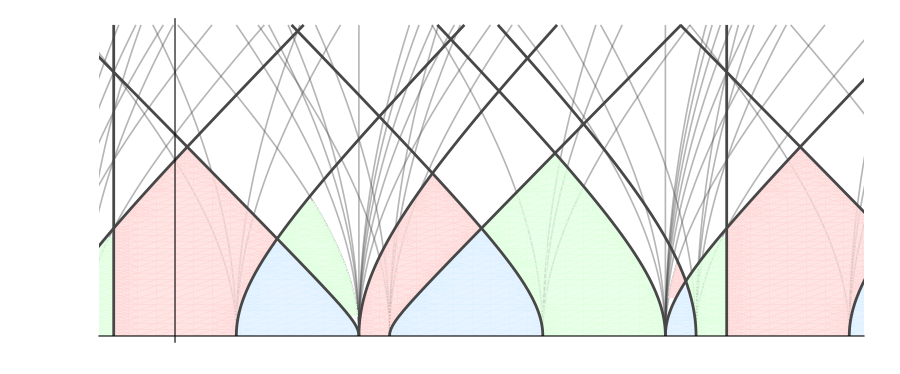

```mathematica
plt=Show[{
ParametricPlot[otherrays, {t,0,0.5},
PlotStyle->Directive[Thickness[.0013],RGBColor[0.28, 0.28, 0.28], Opacity[.4]]
],
dBr,
dAI,
dAII,
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28]
](*,
Graphics[{Red, GamLabel[-Ch[-1,-1], -1/10, 0, "\\mathcal{O}(-1,-1)[1]", .4]}]*)
},
PlotRange->{{-.1, 1.1},{0,0.5}},
AspectRatio->Automatic,
Frame->False,
Axes->{True,False},
Ticks->{ticks,None},
ImageSize->900
]
```

```mathematica
(*FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "LVRasterize_m_m1_10.pdf"], %]*)
```

/Users/rishi/Developer/localf1/figures/LargeVolume/LVRasterize_m_m1_10.pdf

```mathematica
GamLabel[gam_, m_, psi_, string_, t0_]:=Module[{r=(gam/.repCh)[[1]]},Text[MaTeX["\\textcolor{gamcolor}{"<>string<>"}"], {Rays[gam/.repCh, #,psi,m], #}&[t0], {0,-1}, -Sign[If[r!=0,r,-1]]Normalize[{D[Rays[gam/.repCh, t,psi,m],t]/.{t->t0}, 1}]]];
```

```mathematica
labels=With[{m=4/10,psi=0},{
GamLabel[Ch[0,0], m, psi, "\\mathcal{O}(0,0)", .08],
GamLabel[Ch[1,0], m, psi, "\\mathcal{O}(1,0)", .33],
GamLabel[Ch[1,1], m, psi, "\\mathcal{O}(1,1)", .25],
GamLabel[-Ch[-1,0], m, psi, "\\mathcal{O}(-1,0)[1]", .37],
GamLabel[-Ch[0,1], m, psi, "\\mathcal{O}(0,1)[1]", .35],
GamLabel[Ch[2,2], m, psi, "\\mathcal{O}(2,2)", .22],
GamLabel[-Ch[2,2], m, psi, "\\mathcal{O}(2,2)[1]", .35],
GamLabel[-Ch[0,0], m, psi, "\\mathcal{O}(0, 0)[1]", .2],
GamLabel[Ch[3,2], m, psi, "\\mathcal{O}(3, 2)", .2],
GamLabel[Ch[3,3], m, psi, "\\mathcal{O}(3, 3)", .28],
GamLabel[-Ch[1,1], m, psi, "\\mathcal{O}(1, 1)[1]", .265],
GamLabel[Ch[4,3], m, psi, "\\mathcal{O}(4, 3)", .27],
GamLabel[-Ch[3,2], m, psi, "\\mathcal{O}(3, 2)[1]", .1],
GamLabel[GV[0,1,-1/2], m, psi, "GV\\left(0,1,-\\tfrac12\\right)", .25],
GamLabel[GV[0,1,1/2], m, psi, "GV\\left(0,1,\\tfrac12\\right)", .22],
(* Quiver domains for CollBridgeland *)
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(1,1)"], {.19,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(2,2)"], {.49, .04}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(3,3)"}, Center, -.1], {.826,.03}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(4,3)"}, Center, -.1], {1.14,.04}],
(* Quiver domains for CollArcaraI *)
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(1,1)"}, Center, -.1], {-.13,.09}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(2,1)"}, Center, -.1], {.22,.16}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(3,2)"], {.66,.11}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(4,3)"}, Center, -.1], {.87,.09}],
(* Quiver domains for CollArcaraII *)
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(1,1)"], {0.01,.1}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(2,2)"], {.41,.15}],
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes","\\mathcal{O}(3,3)"}, Center,-.1], {.78,.12}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(4,3)"], {1.01,.1}](**)
}];
plt1=Show[plt, Graphics[labels]]
```

-Graphics-

```mathematica
FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt1, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "Ras_LV_m_4_10.pdf"], %]
```

/Users/rishi/Developer/localf1/figures/LargeVolume/Ras_LV_m_4_10.pdf

```mathematica
Ch[0,0]-Ch[-1,0]/.repCh
```

{0,1,0,0}

```mathematica
Ch[2,1]-Ch[1,1]/.repCh
```

{0,1,0,1}

## XY Plane

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
ch=Flatten@ChernToCh[Table[SpectralFlow[CollInitial[[3]]/.repCh, {3k,2k}], {k,-3,3}]];
in=Simplify@Table[NaiveIntersection[-ch[[k]]/.repCh, ch[[k+1]]/.repCh, m], {k,1,Length[ch]-1}];
lines[m_]=Table[Line[{in[[k]], in[[k+1]]}], {k, 1, Length[in]-1}];
```

```mathematica
labels[m_]=Simplify[Table[Text[With[{tmp=(ch[[k+1]]/.repCh)[[{2,3}]]},MaTeX["\\textcolor{gamcolor}{\\mathcal{O}("<>ToString[tmp[[1]]]<>","<>ToString[tmp[[2]]]<>")}"]], (in[[k]]+in[[k+1]])/2, {0,1.5}, (in[[k+1]]-in[[k]])/{1,14/3}],{k, 1, Length[in]-1}]];
```

```mathematica
XYFan[ch1_, ch2_,m_, Nr_:10]:=Module[{kap,inter,dims},
inter = NaiveIntersection[ch1,ch2, m];
kap=Abs@DSZ[ch1,ch2];
dims=Join[KroneckerDims[kap, Nr], {{1,0}, {0,1}}];
Table[{d.{ch1,ch2}, inter, 0,0,0,0,1}, {d, dims}]
];
```

```mathematica
XYFanRays[ch1_, ch2_, m_, Nr_:10, len_:20]:=Module[{kap,rays,cmap},
kap=Abs@DSZ[ch1,ch2];
rays=XYFan[ch1,ch2,m,Nr];
cmap=<|
1->RGBColor[0.179, 0.449, 0.9390000000000001],
2->RGBColor[0.101, 0.877, 0.28800000000000003],
3->RGBColor[0.898, 0.04, 0.254]
|>;
Table[XYRaySegment[ry, m, len, <||>, Directive[Lookup[cmap, kap], Thickness[.0015]]], {ry, rays}]
];
```

```mathematica
legend=LineLegend[{Black,Directive[RGBColor[0.752, 0.038, 0.708],Dashed], RGBColor[0.179, 0.449, 0.9390000000000001], RGBColor[0.101, 0.877, 0.28800000000000003], RGBColor[0.898, 0.04, 0.254]}, MaTeX/@{"\\text{Initial ray}", "\\text{Im(T) = 0}", "\\kappa = 1", "\\kappa = 2", "\\kappa = 3"}]
```

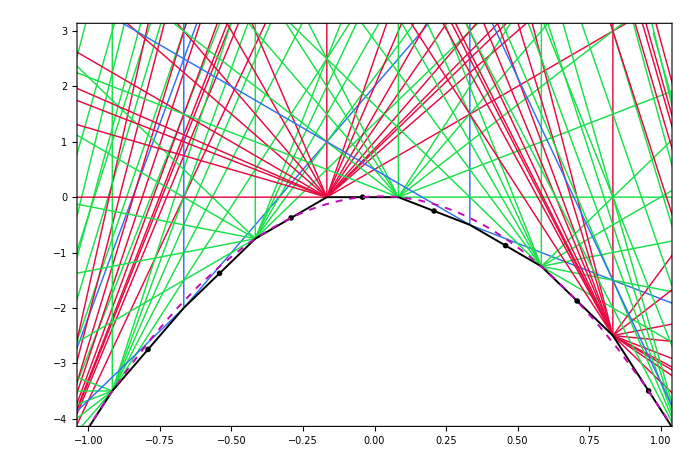

```mathematica
With[{mu=-1/6,  L=4,len=20},
Legended[Show[
Graphics[{
Table[XYFanRays[-ch[[k]]/.repCh,ch[[k+1]]/.repCh, mu], {k,1, Length[ch]-1}]
}],
Graphics[{Thickness[.002],lines[mu], labels[mu]}],
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotStyle->Directive[RGBColor[0.752, 0.038, 0.708], Dashed,Thickness[.002]]
],
PlotRange->{{-1,1},{-4,3}},
PlotRangeClipping->True,
AspectRatio->2/3,
Axes->False,
Frame->True,
ImageSize->700
], Placed[legend, {{1/2,1/5},{1/2,1/2}}]]
]
```

## Boundary Diagram

```mathematica
SpectralFlow[GV[0,1,1/2]/.repCh,{p,q}]
```

{0,0,1,1/2+p-q}

```mathematica
Simplify@InitialPositionNoTest[{0,0,1,1/2+p-q},m]
```

1/2+m+p-q

```mathematica
Expand@Simplify[InitialPositionNoTest[Ch[p,q]/.repCh,m], 3 m+2 p-3 q∈Reals]
%/.{{Abs[x_]:>x},{Abs[x_]:>-x}}//Simplify
```

-m/8+p/4+q/8-1/8 Abs[3 m+2 p-3 q]

{1/2 (-m+q),1/4 (m+2 p-q)}

```mathematica
Simplify@Reduce[3 m+2 p-3 q<0,m]
```

(p|q)∈ℝ&&m+(2 p)/3<q

```mathematica
<<MaTeX`;
cpalette={RGBColor[0.12157,0.46667,0.70588],RGBColor[1.0,0.49804,0.0549],RGBColor[0.17255,0.62745,0.17255],RGBColor[0.83922,0.15294,0.15686],RGBColor[0.58039,0.40392,0.74118],RGBColor[0.54902,0.33725,0.29412],RGBColor[0.8902,0.46667,0.76078],RGBColor[0.49804,0.49804,0.49804],RGBColor[0.73725,0.74118,0.13333],RGBColor[0.0902,0.7451,0.81176]};
```

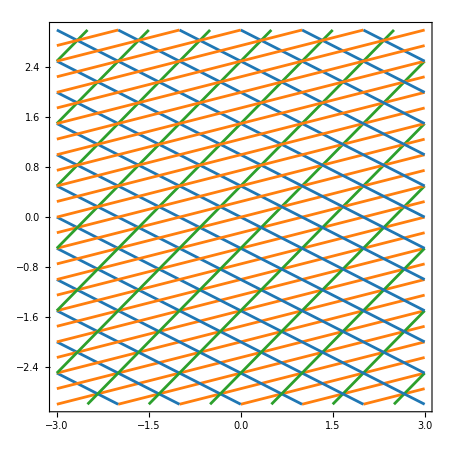

```mathematica
rays=With[{L=15},
Flatten@Table[{Style[(a1-m)/2,cpalette[[1]]], Style[(a1+m)/4, cpalette[[2]]],Style[1/2+m+a1, cpalette[[3]]]}, {a1,-L, L}]];
plt=Plot[
rays,
{m,-3,3}, 
PlotStyle->Black, 
PlotRange->{{-3,3},{-3,3}}, 
AspectRatio->Automatic,
Frame->True,
FrameLabel->MaTeX/@{"m", "T"},
GridLines->{Range[-3,3,1/3],Range[-3,3,1/6]},
PlotHighlighting->None
]
```

```mathematica
Solve[{tf==2t+m,tb==t-m},{t,m}]
```

{{t→(tb+tf)/3,m→1/3 (-2 tb+tf)}}

```mathematica
Simplify[t-(1/2+m+a1)/.{t->(tb+tf)/3,m->1/3 (-2 tb+tf)}]
{tf,tb}/.First@Solve[%==0,tb]//Expand
```

-1/2-a1+tb

{tf,1/2+a1}

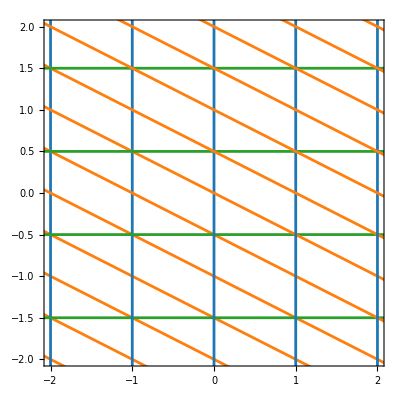

```mathematica
rays=With[{L=10},
Flatten@Table[{Style[{a1,u},cpalette[[1]]], Style[{u,(a1-u)/2}, cpalette[[2]]],Style[{u,1/2+a1}, cpalette[[3]]]}, {a1,-L, L}]];
ParametricPlot[
rays,
{u,-5,5}, 
PlotStyle->Black, 
PlotRange->{{-2,2},{-2,2}}, 
AspectRatio->Automatic,
Frame->True,
FrameLabel->MaTeX/@{"m", "T"},
GridLines->{Range[-2,2,1/3],Range[-2,2,1/6]},
PlotHighlighting->None
]
```

```mathematica
Simplify[{1,1+1}.{Ch[3,1],-Ch[2,1]}/.repCh]
```

{-1,-1,-1,-1/2}

```mathematica
Simplify[{k+1,k}.{Ch[3,1],-Ch[2,1]}/.repCh]
```

{1,3+k,1,5/2+k}

```mathematica
Simplify[{k,k+1}.{Ch[2,1],-Ch[1,1]}/.repCh]
```

{-1,-1+k,-1,-1/2+k}

```mathematica
1-k==3
```

```mathematica
Simplify[{k,k+1}.{Ch[3,2],-Ch[2,2]}/.repCh]
Solve[%==(-Ch[2,1]/.repCh), k]
```

{-1,-2+k,-2,2 (-1+k)}

{}

```mathematica
Simplify[{k,k+1}.{Ch[3,1],-Ch[2,1]}/.repCh]
Solve[%==(-Ch[0,1]/.repCh), k]
```

{-1,-2+k,-1,-3/2+k}

{{k→2}}

```mathematica
{k,k+1}.{Ch[3,1],-Ch[2,1]}/.repCh/.{k->2}
```

{-1,0,-1,1/2}

```mathematica
Simplify[{k,k+1}.{Ch[3+p,1],-Ch[2+p,1]}/.repCh/.{k->p+2}]
```

{-1,0,-1,1/2}

```mathematica
FullSimplify[Reduce[And@@Thread[ComplexExpand[Re[ZLV[#,s,m]]&/@SpectralFlow[CollBridgeland,{mf,mb}]]<0],{s,m}],{(s|m)∈Reals,(mf|mb)∈Integers}]
```

(1+6 s≤2 mf&&1+m+2 s>mb&&m+2 mf<1+mb+4 s)||(2 mf<1+6 s&&m+2 mf>mb+4 s&&m+2 s<mb)

```mathematica
FullSimplify[Reduce[And@@Thread[ComplexExpand[Re[ZLV[#,s,m]]&/@SpectralFlow[CollArcaraI,{mf,mb}]]<0],{s,m}],{(s|m)∈Reals,(mf|mb)∈Integers}]
```

m+mf>1/2+mb+s&&((1/2<mf-3 s<1&&m+2 s<mb)||(1≤mf-3 s<3/2&&m+2 mf<2+mb+4 s))

```mathematica
FullSimplify[Reduce[And@@Thread[ComplexExpand[Re[ZLV[#,s,m]]&/@SpectralFlow[CollArcaraII,{mf,mb}]]<0],{s,m}],{(s|m)∈Reals,(mf|mb)∈Integers}]
```

m+mf<1/2+mb+s&&((m+2 mf>1+mb+4 s&&1/2<mf-3 s<1)||(1+m+2 s>mb&&1≤mf-3 s<3/2))

```mathematica
ineqBr=Flatten[Table[((1+6 s≤2 mf&&1+m+2 s>mb&&m+2 mf<1+mb+4 s)||(2 mf<1+6 s&&m+2 mf>mb+4 s&&m+2 s<mb)), {mf,-2,3},{mb,-2,3}]];
ineqAI=Flatten[Table[m+mf>1/2+mb+s&&((1/2<mf-3 s<1&&m+2 s<mb)||(1≤mf-3 s<3/2&&m+2 mf<2+mb+4 s)), {mf,-2,3},{mb,-2,3}]];
ineqAII=Flatten[Table[m+mf<1/2+mb+s&&((m+2 mf>1+mb+4 s&&1/2<mf-3 s<1)||(1+m+2 s>mb&&1≤mf-3 s<3/2)), {mf,-2,3},{mb,-2,3}]];
```

```mathematica
ineqBr1=FullSimplify[And[Or@@ineqBr, -1<s<1,-1<m<1], (s|m)∈Reals];
ineqAI1=FullSimplify[And[Or@@ineqAI, -1<s<1,-1<m<1], (s|m)∈Reals];
ineqAII1=FullSimplify[And[Or@@ineqAII, -1<s<1,-1<m<1], (s|m)∈Reals];
```

$Aborted

```mathematica
plt1=RegionPlot[{ineqBr1, Or@@ineqAI, Or@@ineqAII}, {m,-1,1},{s,-1,1},
PlotStyle->{Opacity[.2,cpalette[[5]]], Opacity[.2, cpalette[[6]]], Opacity[.2, cpalette[[7]]]},
BoundaryStyle->None,
PlotPoints->40
]
```

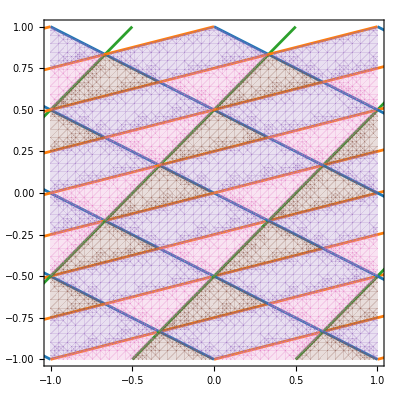

```mathematica
Show[plt,plt1]
```

## Initial s value and state level

```mathematica
(*ClearAll[sameNumQ];
sameNumQ[a_,b_,tol_:10^-12]:=TrueQ[Chop[N[a-b],tol]==0];*)
```

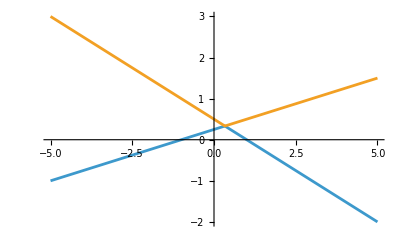
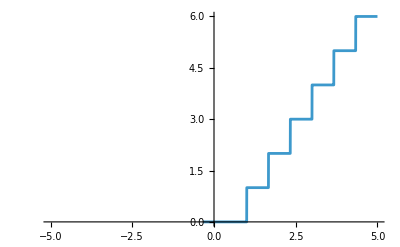
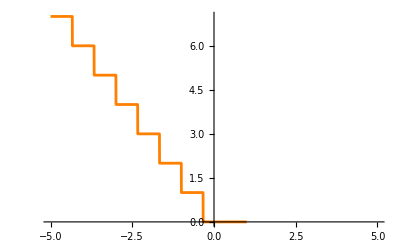

```mathematica
With[{df=1,db=1},{
Plot[{First[Initials[Ch[df,db]/.repCh, m, "Verbose"->False]], First[Initials[-Ch[df,db]/.repCh, m, "Verbose"->False]]}, {m,-5,5}],
Plot[Last[Initials[Ch[df,db]/.repCh, m, "Verbose"->False]], {m,-5,5}],
Plot[Last[Initials[-Ch[df,db]/.repCh, m, "Verbose"->False]], {m,-5,5}, PlotStyle->Orange]}]
```

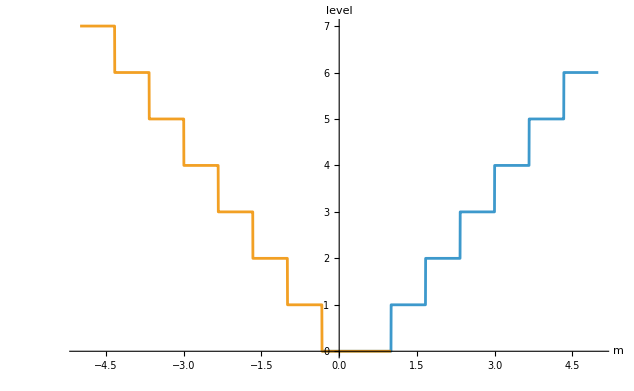

```mathematica
With[{df=1,db=1},
Plot[{Last[Initials[Ch[df,db]/.repCh, m, "Verbose"->False]],Last[Initials[-Ch[df,db]/.repCh, m, "Verbose"->False]]}, {m,-5,5}, AxesLabel->{"m","level"}]]
```

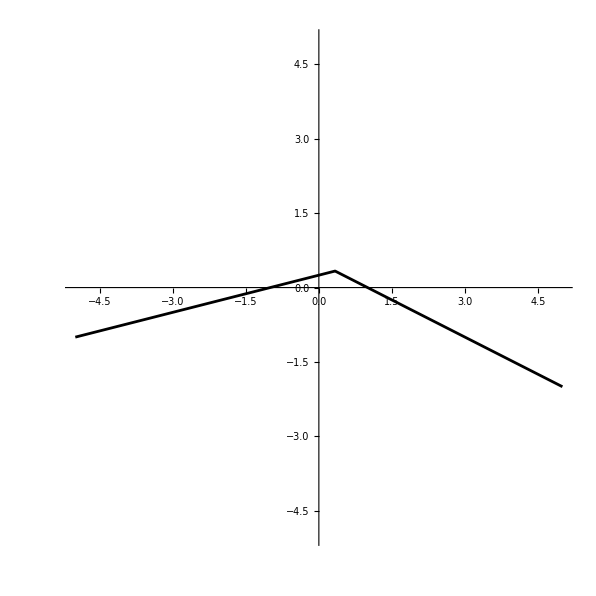

```mathematica
Plot[First[Initials[Ch[1,1]/.repCh, m, "Verbose"->False]], {m,-5,5},PlotStyle->Black,PlotRange->{{-5,5},{-5,5}},AspectRatio->1]
```

```mathematica
Initials[Ch[1,1]/.repCh, -11/10]
```

m = -11/10, q = -1, m1 = -1/10, s = -1/40, k = -1, s1 = 39/40

standardized = {1,4,4,8}, expected = Ch[3,2]

{-1/40,Missing[DoesNotReachBdy]}

```mathematica
ClearAll[sInitials,levelInitials,integerValuedQ,validLevelQ,goodSamplePoint,decoratePlot];

sInitials[gam_, m_?NumericQ]:=Initials[gam/. repCh,m,"Verbose"->False][[1]];
levelInitials[gam_, m_?NumericQ]:=Initials[gam/. repCh,m,"Verbose"->False][[2]];

integerValuedQ[x_]:=IntegerQ[x]||(NumericQ[x]&&x==Round[x]);

validLevelQ[gam_,x_?NumericQ]:=integerValuedQ[Quiet[levelInitials[gam, x]]];

goodSamplePoint[gam_, {a_,b_}]:=Module[{mid,h,offsets,pts},mid=(a+b)/2;
h=b-a;
offsets=SortBy[{-1,1,-2,2,-3,3,-4,4}/100,Abs];
pts=mid+h*offsets;
pts=Select[pts,a<#<b&&validLevelQ[gam, #]&];
If[pts==={},Missing["NoGoodSample"],First[pts]]];

Options[decoratePlot]={"Color"->ColorData[97,1]};
decoratePlot[gam_, mmin_,mmax_, OptionsPattern[]]:=Module[{eps=10^-6,gap=.03,candidates,baseCuts,allCuts,intervals,validIntervals,pieces,labels,endpoints},(*all possible special points n/3 inside the plotting window*)
candidates=Select[Range[Ceiling[3 mmin]/3,Floor[3 mmax]/3,1/3],mmin<#<mmax&];
(*cut either where validity changes or where the integer level jumps*)baseCuts=Select[candidates,Quiet[validLevelQ[gam, #-eps]]=!=Quiet[validLevelQ[gam, #+eps]]||(validLevelQ[gam, #-eps]&&validLevelQ[gam, #+eps]&&Quiet[levelInitials[gam, #-eps]]=!=Quiet[levelInitials[gam, #+eps]])&];
allCuts=Sort@DeleteDuplicates@Join[{mmin},baseCuts,{mmax}];
intervals=Partition[allCuts,2,1];
(*keep only intervals that contain at least one safe interior sample point*)
validIntervals=Select[intervals,goodSamplePoint[gam, #]=!=Missing["NoGoodSample"]&];
pieces=Map[Module[{a=#[[1]],b=#[[2]],g},g=Min[gap,N[(b-a)/10]];
If[a+g<b-g,Plot[sInitials[gam, m],{m,N[a+g],N[b-g]},PlotStyle->{OptionValue["Color"],Thickness[.0055]},PlotRange->All],Nothing]]&,validIntervals];
labels=Map[Module[{x=goodSamplePoint[gam, #],lev},lev=levelInitials[gam, x];
Text[Style["k="<>ToString[Round[lev]],13,Black,Background->White,FontFamily->"CMU Sans Serif"],{x,sInitials[gam, x]},{0,-1.5}]]&,validIntervals];
endpoints={EdgeForm[{Black,Thickness[.003]}], White,Disk[#, .03]&/@({#,sInitials[gam,#]}&/@validIntervals[[;;-2,2]])};
(*Show[pieces,Epilog->labels,AxesLabel->{"m","s[m]"},PlotRange->{{-5,5}, {-5,5}}, AspectRatio->1, Frame->True]*)
{pieces,labels,endpoints}];
```

```mathematica
ClearAll[decoratePlotCombined];
Options[decoratePlotCombined] = Join[
   {"BackgroundRays" -> False},
   Options[Graphics]
   ];

decoratePlotCombined[gam_, mmin_, mmax_, opts : OptionsPattern[]] := 
 Module[{rays, plt1, plt2,l0},

  rays = If[
    OptionValue["BackgroundRays"],
    With[{L = 15},
      Flatten@Table[
        {
Style[(a1 - m)/2, {Opacity[.1,cpalette[[1]]], Thickness[.01]}], 
Style[(a1 - m)/2+.02, {Opacity[.4,cpalette[[1]]], Thickness[.002]}], 
Style[(a1 - m)/2-.02, {Opacity[.4,cpalette[[1]]], Thickness[.002]}], 
Style[(a1 + m)/4,cpalette[[2]]], 
Style[1/2 + m + a1, cpalette[[3]]]},
        {a1, -L, L}
      ]
    ],
    {}
  ];

  plt1 = decoratePlot[gam, mmin, mmax, "Color" -> Blue];
  plt2 = decoratePlot[-gam, mmin, mmax, "Color" -> Red];
l0=Join[plt1[[2]], plt2[[2]]];
  Show[
    {
      If[
        OptionValue["BackgroundRays"],
        Plot[
          rays,
          {m, -3, 3},
          PlotStyle -> Directive[Opacity[.4], Thickness[.002]], PlotHighlighting->None
        ],
        Nothing
      ],
      Join[First[plt1], First[plt2]],
      Graphics[Join[Select[l0,FreeQ[#,"k=0",Infinity]&],Take[Select[l0,!FreeQ[#,"k=0",Infinity]&],1]]],
Graphics[Join[Last[plt1],Last[plt2]]]
    },
    Sequence @@ FilterRules[{opts}, Options[Graphics]]
  ]
]
```

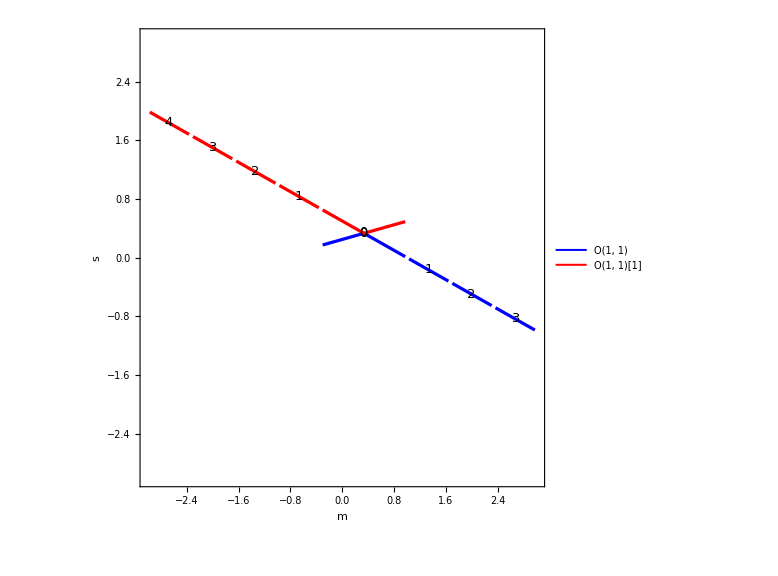

```mathematica
Legended[decoratePlotCombined[Ch[1,1],-3,3, PlotRange->{{-3,3},{-3,3}},AspectRatio->1,Frame->True,FrameLabel->{"m", "s"},ImageSize->Large], Placed[LineLegend[{Directive[Blue,Thickness[.004]], Directive[Red,Thickness[.004]]}, {"O(1, 1)", "O(1, 1)[1]"}], {{.2,.3},{.5,.5}}]]
```

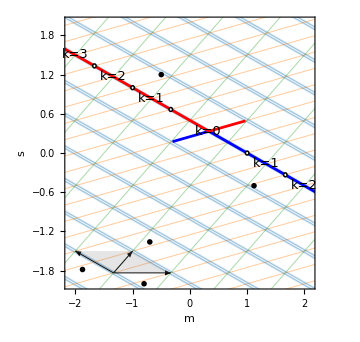

/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-and-Ch11.pdf

```mathematica
Show[
decoratePlotCombined[Ch[1,1],-3,3, PlotRange->{{-2.1,2.1},{-2,2}},AspectRatio->Automatic,Frame->True,Axes->True,Ticks->False,FrameLabel->{"m", "s"},ImageSize->Medium, "BackgroundRays"->True],
Graphics[With[{og={-4/3,-11/6}},{Black, Thickness[.002], Arrow[{og,og+{-2/3,1/3}}],Arrow[{og,og+{1,0}}], Arrow[{og,og+{1/3,1/3}}], EdgeForm[None], FaceForm[Opacity[.2, Gray]],Polygon[{og, og+{-2/3,1/3}, og+{1/3,1/3}, og+{1,0}}]}]],
Graphics[{
Style[Text[MaTeX["\\mathcal{O}(1,1)[1]"], {-.5,1.2}], Background->White], 
Style[Text[MaTeX["\\mathcal{O}(1,1)"], {1.12,-.5}], Background->White],
Style[Text[MaTeX["\\otimes\\mathcal{O}(0,1)"], {-.8,-2}]],
Style[Text[MaTeX["\\otimes\\mathcal{O}(1,1)"], {-.7,-1.36}]],
Style[Text[MaTeX["\\otimes\\mathcal{O}(1,0)"], {-1.89,-1.78}]]
}]
]
If[DirectoryQ["/Users/rishi/Developer/localf1"],Export["/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-and-Ch11.pdf",%]]
```

Better background

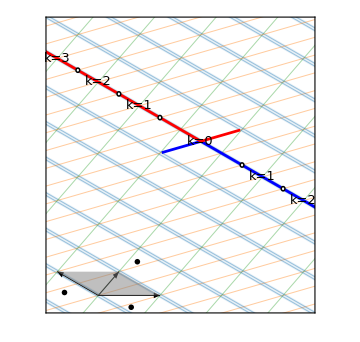

/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-and-Ch11-v2.pdf

```mathematica
Show[
decoratePlotCombined[Ch[1,1],-3,3, PlotRange->{{-2.1,2.1},{-2,2}},AspectRatio->Automatic,Frame->True,Axes->True,Ticks->False,FrameLabel->MaTeX/@{"m", "s"},ImageSize->Medium, "BackgroundRays"->True,FrameTicks->With[{xticks=Range[-2,2], yticks=Range[-2,2]}, {{Thread[{yticks,MaTeX/@yticks}], None}, {Thread[{xticks, MaTeX/@xticks}], None}}]],
Graphics[With[{og={-4/3,-11/6}},{Black, Thickness[.002], Arrow[{og,og+{-2/3,1/3}}],Arrow[{og,og+{1,0}}], Arrow[{og,og+{1/3,1/3}}], EdgeForm[None], FaceForm[Opacity[.5, Gray]],Polygon[{og, og+{-2/3,1/3}, og+{1/3,1/3}, og+{1,0}}]}]],
Graphics[{
(*Style[Text[MaTeX["\\mathcal{O}(1,1)[1]"], {-.5,1.2}], Background->White], 
Style[Text[MaTeX["\\mathcal{O}(1,1)"], {1.12,-.5}], Background->White],*)
Style[Text[MaTeX["\\otimes\\mathcal{O}(0,1)"], {-.8,-2}]],
Style[Text[MaTeX["\\otimes\\mathcal{O}(1,1)"], {-.7,-1.36}]],
Style[Text[MaTeX["\\otimes\\mathcal{O}(1,0)"], {-1.89,-1.78}]]
}]
]
If[DirectoryQ["/Users/rishi/Developer/localf1"],Export["/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-and-Ch11-v2.pdf",%]]
```

```mathematica
<<MaTeX`;
cpalette={RGBColor[0.12157,0.46667,0.70588],RGBColor[1.0,0.49804,0.0549],RGBColor[0.17255,0.62745,0.17255],RGBColor[0.83922,0.15294,0.15686],RGBColor[0.58039,0.40392,0.74118],RGBColor[0.54902,0.33725,0.29412],RGBColor[0.8902,0.46667,0.76078],RGBColor[0.49804,0.49804,0.49804],RGBColor[0.73725,0.74118,0.13333],RGBColor[0.0902,0.7451,0.81176]};
```

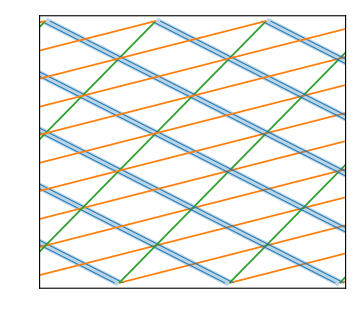

/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-Base2.pdf

```mathematica
defaultStyle={Thickness[.0035]};
rays=With[{L=15},
Flatten@Table[{
Style[(a1-m)/2-.02,{
Sequence@@defaultStyle,
Thickness[.002],
cpalette[[1]]
}],
Style[(a1-m)/2+.02,{
Sequence@@defaultStyle,
Thickness[.002],
cpalette[[1]]
}],
Style[(a1-m)/2,{
Sequence@@defaultStyle,
Thickness[.015],
Opacity[.3,cpalette[[1]]]
}], 
Style[(a1+m)/4, {
Sequence@@defaultStyle,
cpalette[[2]]
}],
Style[1/2+m+a1, {
Sequence@@defaultStyle,
cpalette[[3]]
}]}, {a1,-L, L}]];
plt=Plot[
rays,
{m,-3,3}, 
PlotRange->{{-1,5/3},{-5/6,3/2}}, 
AspectRatio->Automatic,
Frame->True,
FrameLabel->MaTeX/@{"m", "s"},(*
GridLines->{Range[-3,3,1/3],Range[-3,3,1/6]},*)
FrameTicks->With[{xticks=Range[-1,2,.5], yticks=Range[-1,2,.5]}, {{Thread[{yticks,MaTeX/@yticks}], None}, {Thread[{xticks, MaTeX/@xticks}], None}}],
Axes->True,
PlotHighlighting->None,
ImageSize->Medium
]
If[DirectoryQ["/Users/rishi/Developer/localf1"],Export["/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-Base2.pdf",%]]
```

```mathematica
Assuming[m>1/3,Simplify@InitialPositionNoTest[Ch[1,1]/.repCh,m]]
```

(1-m)/2

```mathematica
Solve[(1-m)/2-.02==(1+m)/4,m]
```

{{m→0.306667}}

```mathematica
Solve[(1+m)/4==(1-m)/2+.02]
```

{{m→0.36}}

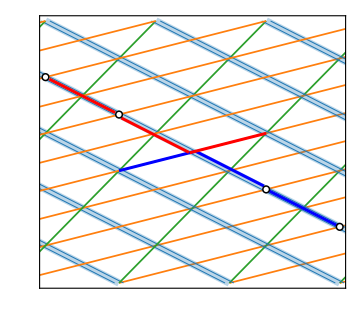

/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-Base3.pdf

```mathematica
p1=decoratePlot[Ch[1,1],-1.1,1.7,"Color"->Blue];
p2=decoratePlot[-Ch[1,1],-1.1,1.7,"Color"->Red];
defaultStyle={Thickness[.006]};
Show[plt, Graphics[Join[p1[[3]], p2[[3]]]],
Plot[(1-m)/2+.02,{m,0.36,1-.02},PlotStyle->{Blue,Sequence@@defaultStyle}],
Plot[(1+m)/4,{m,-1/3,0.36},PlotStyle->{Blue, Sequence@@defaultStyle}], 
Plot[(1+m)/4,{m,0.307,1},PlotStyle->{Red, Sequence@@defaultStyle}],

Plot[sInitials[Ch[1,1],m],{m,1+.03,5/3-0.03},PlotStyle->{Blue, Sequence@@defaultStyle}],
Plot[(1-m)/2-.02,{m,-1/3+.021,0.3},PlotStyle->{Red, Sequence@@defaultStyle}],
Plot[sInitials[-Ch[1,1],m],{m,-1+.035,-1/3-.035},PlotStyle->{Red, Sequence@@defaultStyle}]
]
If[DirectoryQ["/Users/rishi/Developer/localf1"],Export["/Users/rishi/Developer/localf1/figures/LargeVolume/BoundaryRays-Base3.pdf",%]]
```

#### ray direction

```mathematica
(* the ray GV[0, 1, ch2] *)
InitialPositionNoTest[{0,0,1,ch2},m]
```

ch2+m

```mathematica
(* "center" of a ray Ch[p, q] in (m, s) coordinates *)
FullSimplify[InitialPositionNoTest[Ch[p,q]/.repCh,m],{m∈Reals, (p|q)∈Integers}]
Simplify[{q-2p/3,%/.{m->q-2p/3}}]
```

1/8 (-m+2 p+q-Abs[3 m+2 p-3 q])

{-(2 p)/3+q,p/3}

```mathematica
(* direction vector of r Ch[p, q] *)
FullSimplify[InitialPositionNoTest[r Ch[p,q]/.repCh,m], {m∈Reals, (r|p|q)∈Integers}]
FullSimplify[D[%,m], {m∈Reals, (p|q)∈Integers}]
```

1/8 (-m+2 p+q-Abs[3 m+2 p-3 q] Sign[r])

1/8 (-1-3 Sign[3 m+2 p-3 q] Sign[r])

```mathematica
(* no canonical direction for GVs *)
ComplexExpand[Im[ZLV[{0,df,db,ch2},s+I t,m1+I m2]]/Im[s+I t]]
Limit[%, m2->0]
D[%,{{m1,s}}]
```

db+2 df-(db m2)/t+(df m2)/t

db+2 df

{0,0}

```mathematica
(* projection of the direction vector of a ray into gradient of cost function *)
ComplexExpand[Im[ZLV[r Ch[p,q]/.repCh,s+I t,m1+I m2]]/Im[s+I t]]
Limit[%, m2->0]
D[%,{{m1,s}}]
FullSimplify[Sign[%.{8,(-1-Sign[r]3 Sign[3 m+2 p-3 q])}], {m∈Reals, (r|p|q)∈Integers}]
```

-m1 r+2 p r+q r-8 r s+(m1 m2 r)/t+(m2 p r)/t-(m2 q r)/t-(m2 r s)/t

-m1 r+2 p r+q r-8 r s

{-r,-8 r}

Sign[3 m+2 p-3 q] Sign[r]^2

```mathematica
DSZ[Ch[2,1],-Ch[0,1]]/.repCh
```

4

```mathematica
KroneckerDims[4,10]
(#.{Ch[2,1],-Ch[0,1]}&/@%)/.repCh
SecondChernClass/@%
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,3},{2,5},{2,7},{3,1},{3,2},{3,4},{3,5},{3,7},{4,1},{4,3},{4,5},{5,2},{5,3},{5,4},{7,2},{7,3}}

{{0,2,0,2},{-1,2,-1,5/2},{-2,2,-2,3},{-3,2,-3,7/2},{1,4,1,7/2},{-1,4,-1,9/2},{-3,4,-3,11/2},{-5,4,-5,13/2},{2,6,2,5},{1,6,1,11/2},{-1,6,-1,13/2},{-2,6,-2,7},{-4,6,-4,8},{3,8,3,13/2},{1,8,1,15/2},{-1,8,-1,17/2},{3,10,3,17/2},{2,10,2,9},{1,10,1,19/2},{5,14,5,23/2},{4,14,4,12}}

{-2,-5,-9,-14,0,-9,-22,-39,5,0,-13,-21,-40,13,0,-17,17,9,0,46,36}

```mathematica
Table[Simplify[{k,k+1}.{-Ch[1,1],Ch[2,1]}/.repCh], {k,0,5}]
Table[Simplify[{k+1,k}.{-Ch[1,1],Ch[2,1]}/.repCh], {k,0,5}]
```

{{1,2,1,3/2},{1,3,1,5/2},{1,4,1,7/2},{1,5,1,9/2},{1,6,1,11/2},{1,7,1,13/2}}

{{-1,-1,-1,-1/2},{-1,0,-1,1/2},{-1,1,-1,3/2},{-1,2,-1,5/2},{-1,3,-1,7/2},{-1,4,-1,9/2}}

```mathematica
FullSimplify[Rays[r Ch[p,q]/.repCh, t, 0, m]/.{Im[m]->0,Re[m]->m}]
Series[%, {t,0,2}]
```

((-m+2 p+q) r-√(r^2 ((3 m+2 p-3 q)^2+64 t^2)))/(8 r)

((-m+2 p+q) r-√((3 m+2 p-3 q)^2 r^2))/(8 r)-(4 r t^2)/(√((3 m+2 p-3 q)^2 r^2))+O[t]^3

```mathematica
tmp[r_,p_,q_,t_,m_]:=((-m+2 p+q)-Sign[r] √((3 m+2 p-3 q)^2+64 t^2))/8;
```

```mathematica
Rays[{0,0,1,ch2},t,0,m]
```

ch2+Re[m]

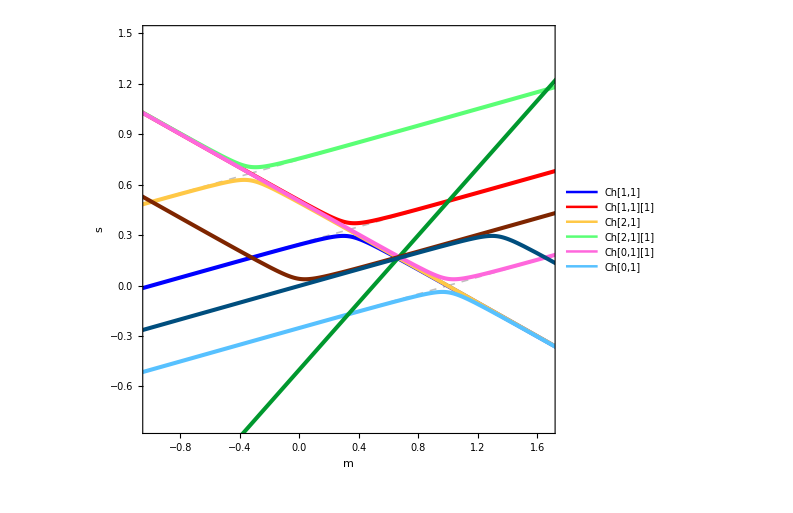

```mathematica
With[{t=.04, th=.005},
Show[
Plot[{tmp[1,1,1,0,m], tmp[-1,1,1,0,m], tmp[1,2,1,0,m],tmp[-1,2,1,0,m], tmp[-1,0,1,0,m],tmp[1,0,1,0,m]}, {m,-2,2},
PlotStyle->{{Thickness[.002],Gray,Dashed, Opacity[.5]}},
PlotRange->{{-1,5/3},{-5/6,3/2}},
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"m","s"}
],
Plot[{tmp[1,1,1,t,m], tmp[-1,1,1,t,m], tmp[1,2,1,t,m],tmp[-1,2,1,t,m], tmp[-1,0,1,t,m],tmp[1,0,1,t,m], -1/2+m, tmp[-1,0,0,t,m], tmp[1,1,2,t,m]}, {m,-2,2},
PlotStyle->{{Thickness[th],Blue}, {Thickness[th],Red},{Thickness[th],RGBColor[1, 0.783, 0.275]}, {Thickness[th],RGBColor[0.353, 1, 0.457]},{Thickness[th],RGBColor[1, 0.402, 0.864]},{Thickness[th], RGBColor[0.341, 0.758, 1]}, {Thickness[th], RGBColor[0, 0.596, 0.18]}, {Thickness[th], RGBColor[0.494, 0.14400000000000002, 0]}, {Thickness[th], RGBColor[0, 0.305, 0.494]}},
PlotLegends->{"Ch[1,1]", "Ch[1,1][1]", "Ch[2,1]","Ch[2,1][1]","Ch[0,1][1]", "Ch[0,1]"}
]]
]
```

```mathematica
DSZ[GV[0,1,-1/2],-Ch[0,1]]/.repCh
```

1

```mathematica
Plus@@{GV[0,1,-1/2],-Ch[0,1]}/.repCh
BogomolovDiscriminant[%]
```

{-1,0,0,0}

0

```mathematica
DSZ[GV[0,1,-1/2],Ch[2,1]]/.repCh
```

-1

```mathematica
Plus@@{GV[0,1,-1/2],Ch[2,1]}/.repCh
BogomolovDiscriminant[%]
```

{1,2,2,1}

1

```mathematica
DSZ[GV[0,1,-1/2],Ch[1,1]]/.repCh
```

-1

```mathematica
DSZ[GV[0,1,-1/2],n1 Ch[1,1]-n2 Ch[0,1]]/.repCh
Simplify[BogomolovDiscriminant[Plus@@{GV[0,1,-1/2], n1 Ch[1,1]-n2 Ch[0,1]}/.repCh]]
%/.{{n1->k,n2->k+1},{n1->k+1,n2->k}}
```

-n1+n2

(-1+n1+n2)/(2 (n1-n2)^2)

{k,k}

```mathematica
Plus@@{GV[0,1,-1/2],Ch[1,1]}/.repCh
BogomolovDiscriminant[%]
```

{1,1,2,0}

0